```mathematica
ClearAll["Global`*"]
```

## settings and definitions

```mathematica
side=20;
 
(* Initialization values for different temperatures
the order is : number of microsteps, number of initial microsteps discarded, side of the lattice model, temperature
*)
settingMe= {7000,0,side,#}&/@Range[1.4,1.4,0.1]
settingWo = {100000,0,side,#}&/@{2.2}
```

(7000 | 0 | 20 | 1.4)

(100000 | 0 | 20 | 2.2)

Required packages

```mathematica
Needs["CCompilerDriver`"]
Needs["ErrorBarPlots`"]
```

Metropolis and Wolff  algorithms

### monte carlo con helical boundary conditions e algoritmo Metropolis

```mathematica
metropolis=Compile[{{steps,_Integer},{eqsteps,_Integer},{lato,_Integer},{temp,_Real}},Block[{matrix,β=1/temp,x,j=1, magnetizzazione,spinsum,delta,random,prob ,yes=0,area=lato^2,precalc,up,down,left,right,counter=1,scalare},
up=RotateLeft[Range[lato^2]]   ;   
         down=RotateRight[Range[lato^2]];
         left=RotateLeft[Range[lato^2],lato];
         right=RotateRight[Range[lato^2],lato];
prob[2]= ⅇ^(-(β*4)); 
prob[4]= ⅇ^(-(β*8));
 
magnetizzazione=ConstantArray[0,Ceiling[(steps-eqsteps+1)/area]];
matrix=Developer`ToPackedArray@RandomChoice[{-1,1},area];
nearestneig= Transpose[{up,down,left,right}];
scalare=Total@matrix ;
Do[
 
yes=0;
random =RandomReal[];
x=RandomInteger[{1,area}];
(*Compile`GetElement[matrix,down[[x]],y]*)

spinsum=Plus@@matrix[[nearestneig[[x]]]];

delta=   spinsum*matrix[[x]];
If[delta<=0,matrix[[x]] = - matrix[[x]];yes=1,
If[random < prob[delta], matrix[[x]]=-matrix[[x]];yes=1
]];
If[yes==1,
scalare= scalare+2*matrix[[x]]];
If[i<=eqsteps ,
magnetizzazione[[1]]=scalare
,


If[Mod[i-eqsteps,area]==0, magnetizzazione[[counter+1]]= scalare  ;++counter       ]
 

]
,{i,2,steps}];
 
N@magnetizzazione/lato^2

]
,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed",CompilationTarget->"C"];
```

```mathematica
(*RepeatedTiming[metropolis[93000,7000,side,2]][[1]]*)
```

### monte carlo (wolff algorithm)

```mathematica
wolff=Compile[{{steps,_Integer},{eqsteps,_Integer},{side,_Integer},{temp,_Real}},Block[{helical,β=1/temp,i, prob ,area=side^2,up,down,left,right,stack,oldspin,sp,sl,current,magnetizzazione},
up=RotateLeft[Range[area]]   ;   
         down=RotateRight[Range[area]];
         left=RotateLeft[Range[area],side];
         right=RotateRight[Range[area],side];
helical=RandomChoice[{-1,1},area];
prob= 1-ⅇ^(-2β);
magnetizzazione=ConstantArray[0,steps-eqsteps];
 Do[
stack= ConstantArray[0,area];
i= RandomInteger[{1,area}];
       stack[[1]]=i;
oldspin= helical[[i]];
helical[[i]]=-helical[[i]];
sp=1;
sl=sp+1;
While[sp<sl,
 
current= stack[[sp]];
sp=sp+1;

If[helical[[up[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= up[[current]];
helical[[up[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[down[[current]]]]== oldspin,
If[RandomReal[]<prob,
 
stack[[sl]]=down[[current]];
helical[[down[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[left[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= left[[current]];
helical[[left[[current]]]]=-oldspin;
sl=sl+1;
]
];
If[helical[[right[[current]]]]== oldspin,
If[RandomReal[]<prob,
stack[[sl]]= right[[current]];
helical[[right[[current]]]]=-oldspin;
sl=sl+1;
]
];
];
If[p>eqsteps,
magnetizzazione[[p-eqsteps]]=Total@helical];

,{p,steps}];
magnetizzazione/area


],Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed",CompilationTarget->"C"];
```

autocorrelation function

```mathematica
autocor [magn_List]:=CorrelationFunction[magn,{Length@magn-1}];
```

## main

```mathematica
ising1=metropolis@@@settingMe;
ising2=wolff@@@settingWo;
```

## Initial Equilibration time

equilibration times: Metropolis

```mathematica
plot=Transpose[{ising1,ConstantArray[6000,Length@settingMe],settingMe[[;;,4]]}];
```

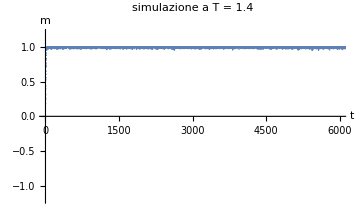
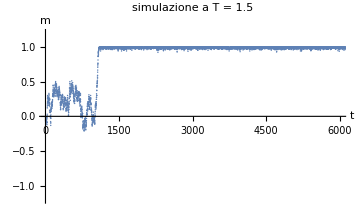

```mathematica
ListPlot[plot[[#,1]],PlotRange->{{0,plot[[#,2]]},{-1.2,1.2}},ImageSize->Medium,AxesLabel->{"t","m"},PlotLabel->"simulazione a T = " <> ToString@plot[[#,3]] ]&/@Range[1,Length@settingMe]
```

equilibration times: Wolff

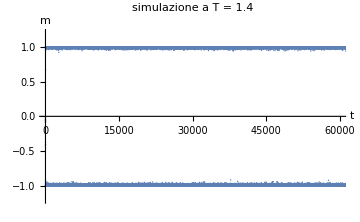
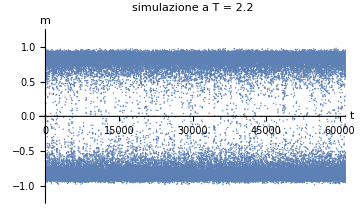
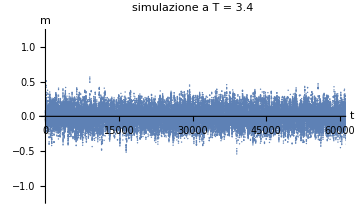

```mathematica
plot=Transpose[{ising2,ConstantArray[60000,Length@settingWo],settingWo[[;;,4]]}];

ListPlot[plot[[#,1]],PlotRange->{{0,plot[[#,2]]},{-1.2,1.2}},ImageSize->Medium,AxesLabel->{"t","m"},PlotLabel->"simulazione a T = " <> ToString@plot[[#,3]] ]&/@Range[1,Length@settingWo]
```

## Autocorrelation plot

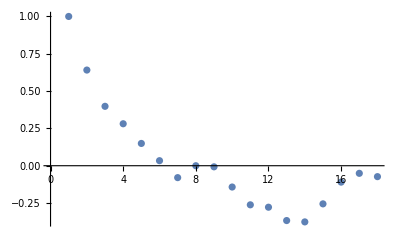

```mathematica
ListPlot[autocor[#]]&/@ ising1
```